```mathematica
(*Parameters*)
ClearAll["Global`*"]
μ=1;
a=1;
l=1;
λ = 20;

(* Find the poles of S, for now have to manually copy/paste the narrowest one into kres below *)
A[g_,l_,k_]:=k*g*a^2*(SphericalBesselJ[l,k*a])^2/(1-I*k*g*a^2*SphericalBesselJ[l,k*a]*SphericalHankelH1[l,k*a]);
Adenom[g_,l_,k_]:=1-I*k*g*a^2*SphericalBesselJ[l,k*a]*SphericalHankelH1[l,k*a];
NSolve[Adenom[λ,l,k]==0 && Abs[k]<10,k]
```

{{k→-8.06304-0.128157 ⅈ},{k→-4.7143-0.0506794 ⅈ},{k→0.-0.946729 ⅈ},{k→0.+9.89793 ⅈ},{k→4.7143-0.0506794 ⅈ},{k→8.06304-0.128157 ⅈ}}

-Graphics-

-Graphics-

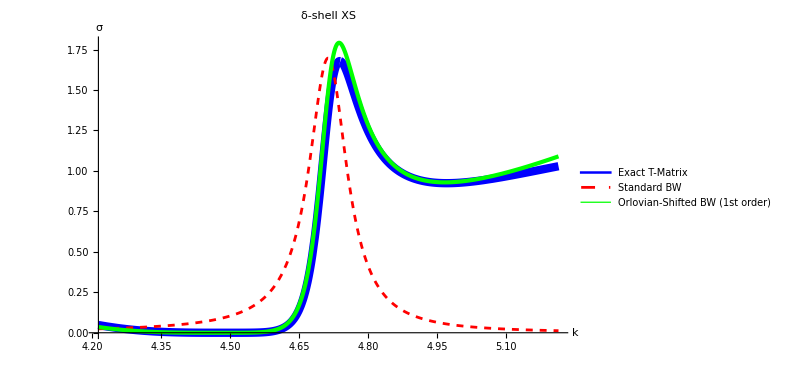

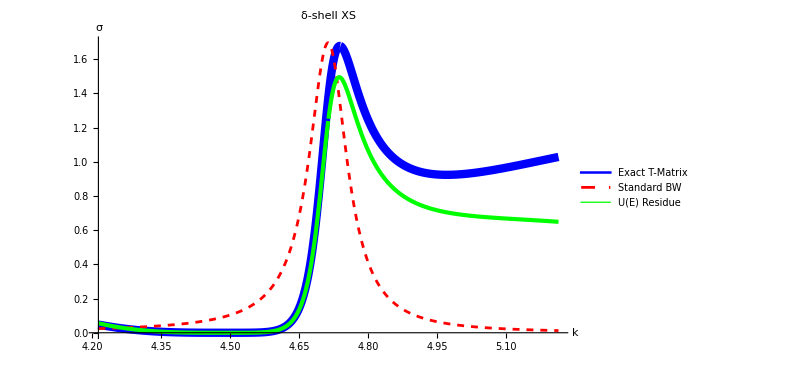

```mathematica
(* Set kres here *)
kres=(4.714304496999773-0.05067937205151212 ⅈ);
kresreal = Re[kres];
Eres=kres^2/(2μ);
buffer = 1;

(* Exact δ-shell T matrix and λ' modified coupling used in Ψ_U *)
T[g_,L_,u_,p_,q_]=-((g*a^2)/(4*Pi^2*μ))*(SphericalBesselJ[L,p*a]*SphericalBesselJ[L,q*a])/(1-I*u*g*a^2*SphericalBesselJ[L,u*a]*SphericalHankelH1[L,u*a]);
λprime[g_,L_,u_]=λ/(1+I*2*u*g*a^2*(SphericalBesselJ[L,u*a])^2);

(*Define Ψ_U and the Factorized T Matrix Note the -k in λ due to the PsiU function being an eigenvector of -kres*)
Psi[g_,L_,u_,p_]=-4*Pi*g*a^2*SphericalBesselJ[L,p*a]*SphericalBesselJ[L,u*a]/(u^2-p^2);
PsiU[g_,L_,u_,p_]=-4*Pi*λprime[g,L,-u]*a^2*SphericalBesselJ[L,p*a]*SphericalBesselJ[L,u*a]/(u^2-p^2);
(*NormTestSquared = 1/NIntegrate[(k^2*PsiU[λ,l,kres,k]^2),{k,0,kresreal,Infinity},Method->"ExtrapolatingOscillatory",MaxRecursion->30](*Define Psi=Psi*NormTestSquared to normalize, and split integral at the resonance to avoid weird numerical issues*)
PsiU[g_,L_,u_,p_]=PsiU[g,L,u,p]*Sqrt[NormTestSquared];
NIntegrate[p^2*PsiU[λ,l,kres,p]^2,{p,0,kresreal,Infinity},Method->"ExtrapolatingOscillatory",MaxRecursion->30]*)
(*PsiUTilde[g_,L_,u_,p_]=-4*Pi*λprime[g,L,-u]*a^2*NormTestSquared*SphericalBesselJ[L,p*a]*SphericalBesselJ[L,u*a];*)
PsiUTilde[g_,L_,u_,p_]=(u^2-p^2)*PsiU[g,L,u,p];
TFactorized[g_,L_,u_,p_,q_]=(1/(2μ))^2PsiUTilde[λ,L,kres,p]*PsiUTilde[λ,L,kres,q]/(kres^2-u^2);

(*Calculate reside at pole so that the factorized version matches, were doing this instead of dealing with weird normalization BS *)
ExactTResidue := (-((λ*a^2)/(4*Pi^2*μ))*(SphericalBesselJ[l,z*a]*SphericalBesselJ[l,z*a])/.z->kres)/(D[(1-I*z*λ*a^2*SphericalBesselJ[l,z*a]*SphericalHankelH1[l,z*a]),z]/.z->kres);
UnscaledFactTResidue := (1/(2μ))^2*PsiUTilde[λ,l,kres,kres]^2/(2kres); (* Doing things so that its normalized to 1 *)
NNsq=UnscaledFactTResidue/ExactTResidue;
TFactorized[g_,L_,u_,p_,q_]=TFactorized[g,L,u,p,q]/NNsq;

(*Plot exact T vs Factorized T (Fake Normalize by matching the peaks just for graphical clarity...)*)
AbsArgPlot[{T[λ,l,z,z,z],TFactorized[λ,l,z,z,z](**(T[λ,l,kresreal,kresreal,kresreal]/TFactorized[λ,l,kresreal,kresreal,kresreal])*)},{z,kresreal-buffer,kresreal+2*buffer},PlotStyle->{{},{Dashed} },PlotLabel->"Solid=Exact T, Dashed=Factorized T",AxesLabel->{"k",""},ImageSize->300]
AbsArgPlot[{T[λ,l,z,z,z]-TFactorized[λ,l,z,z,z](**(T[λ,l,kresreal,kresreal,kresreal]/TFactorized[λ,l,kresreal,kresreal,kresreal])*)},{z,kresreal-buffer,kresreal+2*buffer},PlotStyle->{{}},PlotLabel->"Solid=Exact T, Dashed=Factorized T",AxesLabel->{"k"},ImageSize->300]

(* Define Exact XS and BW XS *)
XS[g_,L_,u_]=(64Pi^5μ^2)*(2L+1)*Abs[T[g,L,u,u,u]]^2;
XSFactorized[g_,L_,u_]=(64Pi^5μ^2)*(2L+1)*Abs[TFactorized[g,L,u,u,u]]^2;
BW[g_,L_,u_]=(4Pi/u^2)(2L+1)*Im[Eres]^2/((u^2/(2μ)-Re[Eres])^2+Im[Eres]^2);

(* Find the Taylor Expansion Coefficients (currently up to 2nd order) and Define Modified XS up to 1st and 2nd Order*)
c1=(D[PsiUTilde[λ,l,kres,z],z]/.z->kres)/PsiUTilde[λ,l,kres,kres];
c2=((D[PsiUTilde[λ,l,kres,z],{z,2}]/.z->kres)/PsiUTilde[λ,l,kres,kres])/2;
XSExpansion1[g_,L_,k_]=BW[g,L,k]*Abs[1+(k-kres)*c1]^4;
XSExpansion2[g_,L_,k_]=BW[g,L,k]*Abs[1+(k-kres)*c1+(k-kres)^2*c2]^4;

(* Plot Exact, BW, and Modified XS's to Compare*)
Plot[{XS[λ,l,z],BW[λ,l,z],XSExpansion1[λ,l,z](*,XSExpansion2[λ,l,z]*)},{z,kresreal-0.5buffer,kresreal+0.5*buffer},PlotStyle->{{Blue,Thickness[0.01]},(*Exact:Thick Blue*){Red,Dashed},(*Standard BW:Dashed Red*){Green,Thickness[0.005]}     (*Perturbative 1st order:Thin Green*)(*,{Orange,Thickness[0.005]}     (*Perturbative 2nd order:Thin Orange*)*)},PlotLegends->{"Exact T-Matrix","Standard BW","Orlovian-Shifted BW (1st order)"(*,"Orlovian-Shifted BW (2nd order)"*)},AxesLabel->{"k","σ"}, PlotLabel->"δ-shell XS",ImageSize->600]
Plot[{XS[λ,l,z],BW[λ,l,z],XSFactorized[λ,l,z](*,XSExpansion2[λ,l,z]*)},{z,kresreal-0.5buffer,kresreal+0.5*buffer},PlotStyle->{{Blue,Thickness[0.01]},(*Exact:Thick Blue*){Red,Dashed},(*Standard BW:Dashed Red*){Green,Thickness[0.005]}     (*Perturbative 1st order:Thin Green*)(*,{Orange,Thickness[0.005]}     (*Perturbative 2nd order:Thin Orange*)*)},PlotLegends->{"Exact T-Matrix","Standard BW","U(E) Residue"(*,"Orlovian-Shifted BW (2nd order)"*)},AxesLabel->{"k","σ"}, PlotLabel->"δ-shell XS",ImageSize->600]
```

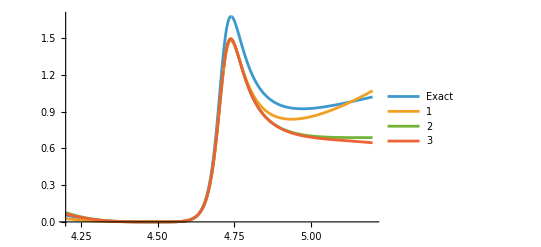

-Graphics-

```mathematica
(*NN=PsiUTilde[λ,l,kres,kres]/(Sqrt[-2 μ*Im[Eres]]); (*Normalize PsiUTilde at the peak artificially*)*)

k[g_,L_,n_]=1/(n!)*D[PsiUTilde[g,L,kres,z],{z,n}]/. z->kres;

PsiUTildePoly[g_,L_,p_,n_]:=Sum[k[g,L,i]*(p-kres)^i,{i,0,n}];

TMatrixPoly[g_,L_,p_,n_]:=(1/(2μ)^2)PsiUTildePoly[λ,l,p,n]^2/(NNsq(kres^2-p^2));

(*Use unitary limit prefactor since T is normalized to 1 at the pole*)
XSPoly[g_,L_,p_,n_]:=(64 Pi^5 μ^2)*(2 L+1)(*(4Pi/p^2)(2L+1)*)*Abs[TMatrixPoly[g,L,p,n]]^2;

Plot[{XS[λ,l,z],XSPoly[λ,l,z,1],XSPoly[λ,l,z,2],XSPoly[λ,l,z,3]},{z,4.2,5.2},PlotLegends->{"Exact","1","2","3"}]
AbsArgPlot[{TMatrixPoly[λ,l,z,2],TFactorized[λ,l,z,z,z](**(T[λ,l,kresreal,kresreal,kresreal]/TFactorized[λ,l,kresreal,kresreal,kresreal])*)},{z,kresreal-buffer,kresreal+buffer},PlotStyle->{{},{Dashed} },PlotLabel->"Solid=Exact T, Dashed=Factorized T",AxesLabel->{"k",""},ImageSize->300]
```

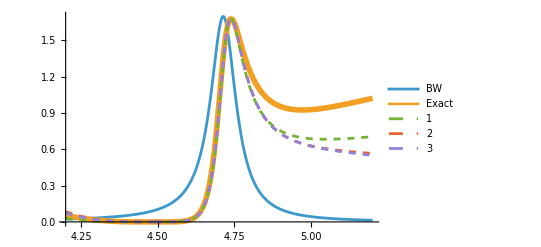

```mathematica
(* K MATRIX APPROACH!!!!!!!!!!!!!!!!!! Find the inverse K matrix to avoid expanding around a pole, then reinvert to get K *)
KMatrixInversePoly[g_,L_,p_,n_]:=Re[1/TMatrixPoly[g,L,p,n]];
KMatrixInverseFactorized[g_,L_,p_]=Re[1/TFactorized[g,L,p,p,p]];
XSKMatrixInversePoly[g_,L_,p_,n_]:=(64 Pi^5 μ^2)*(2 L+1)(*(4Pi/p^2)(2L+1)*)*1/(KMatrixInversePoly[g,L,p,n]^2+(4*Pi^2*μ*p)^2)

(* Because of the 0 at 4.4, ROC is confined to at most 0.3, which is probably why the tails arent great here, but it nails the peak at least!*)
Plot[{BW[λ,l,z],XS[λ,l,z],XSKMatrixInversePoly[λ,l,z,1],XSKMatrixInversePoly[λ,l,z,2],XSKMatrixInversePoly[λ,l,z,3]},{z,4.2,5.2},PlotStyle->{{},{Thickness[0.01]},{Dashed},{Dashed},{Dashed}},PlotLegends->{"BW","Exact","1","2","3"}]
```

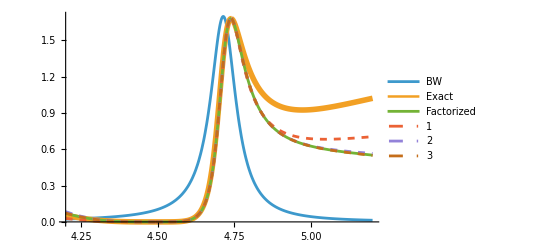

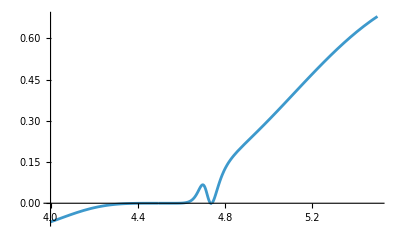

```mathematica
(* Re invert the inverse K matrix to get K*)
KMatrixPoly[g_,L_,p_,n_]:=1/KMatrixInversePoly[g,L,p,n]
KMatrixFactorized[g_,L_,p_]=1/KMatrixInverseFactorized[g,L,p];
XSKMatrixPoly[g_,L_,p_,n_]:=(64 Pi^5 μ^2)*(2 L+1)(*(4Pi/p^2)(2L+1)*)*KMatrixPoly[g,L,p,n]^2/(1+(4*Pi^2*μ*p*KMatrixPoly[g,L,p,n])^2)
XSKMatrixFactorized[g_,L_,p_]=(64 Pi^5 μ^2)*(2 L+1)(*(4Pi/p^2)(2L+1)*)*KMatrixFactorized[g,L,p]^2/(1+(4*Pi^2*μ*p*KMatrixFactorized[g,L,p])^2);
Plot[{BW[λ,l,z],XS[λ,l,z],XSKMatrixFactorized[λ,l,z],XSKMatrixPoly[λ,l,z,1],XSKMatrixPoly[λ,l,z,2],XSKMatrixPoly[λ,l,z,3]},{z,4.2,5.2},PlotStyle->{{},{Thickness[0.01]},{},{Dashed},{Dashed},{Dashed}},PlotLegends->{"BW","Exact","Factorized","1","2","3"}]
Plot[XS[λ,l,z]-XSKMatrixFactorized[λ,l,z],{z,4,5.5}]
```

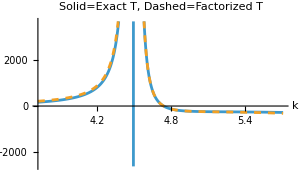

```mathematica
(*Hmmm, seems that constructing KMatrixFactorized directly from TFactorized is bad... must first find Inverse K matrix by taking real component of TFactorized and then inverting to find K, I guess that avoids weird pole issues???? Weird...*)
Plot[{KMatrixInversePoly[λ,l,z,2],Re[1/TFactorized[λ,l,z,z,z]](**(T[λ,l,kresreal,kresreal,kresreal]/TFactorized[λ,l,kresreal,kresreal,kresreal])*)},{z,kresreal-buffer,kresreal+buffer},PlotStyle->{{},{Dashed} },PlotLabel->"Solid=Exact T, Dashed=Factorized T",AxesLabel->{"k",""},ImageSize->300]
```

-Graphics-

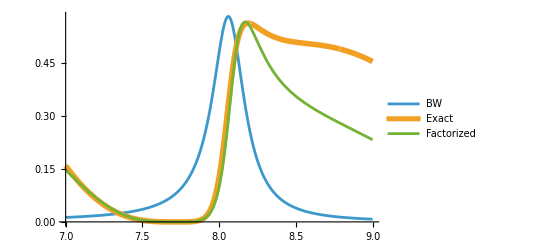

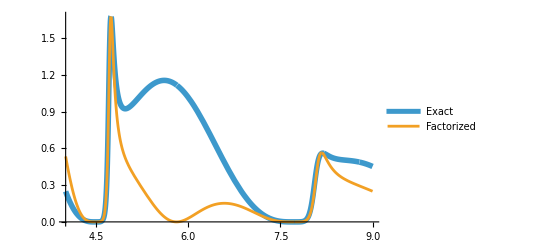

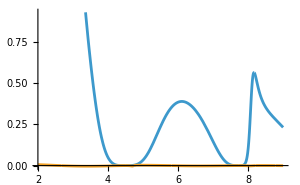

```mathematica
(* Lets try adding in the next resonance *)
kres2=(8.063042352489518-0.12815691814454724 ⅈ);
kresreal2 = Re[kres2];
Eres2=kres2^2/(2μ);
TFactorized2[g_,L_,u_,p_,q_]=(1/(2μ))^2PsiUTilde[λ,L,kres2,p]*PsiUTilde[λ,L,kres2,q]/(kres2^2-u^2);
ExactTResidue2 := (-((λ*a^2)/(4*Pi^2*μ))*(SphericalBesselJ[l,z*a]*SphericalBesselJ[l,z*a])/.z->kres2)/(D[(1-I*z*λ*a^2*SphericalBesselJ[l,z*a]*SphericalHankelH1[l,z*a]),z]/.z->kres2);
UnscaledFactTResidue2 := (1/(2μ))^2*PsiUTilde[λ,l,kres2,kres2]^2/(2kres2); (* Doing things so that its normalized to 1 *)
NNsq2=UnscaledFactTResidue2/ExactTResidue2;
TFactorized2[g_,L_,u_,p_,q_]=TFactorized2[g,L,u,p,q]/NNsq2;
AbsArgPlot[{T[λ,l,z,z,z],TFactorized2[λ,l,z,z,z](**(T[λ,l,kresreal,kresreal,kresreal]/TFactorized[λ,l,kresreal,kresreal,kresreal])*)},{z,kresreal2-2*buffer,kresreal2+2*buffer},PlotStyle->{{},{Dashed} },PlotLabel->"Solid=Exact T, Dashed=Factorized T",AxesLabel->{"k",""},ImageSize->300]

KMatrixInverseFactorized2[g_,L_,p_]=Re[1/TFactorized2[g,L,p,p,p]];
KMatrixFactorized2[g_,L_,p_]=1/KMatrixInverseFactorized2[g,L,p];
XSKMatrixFactorized2[g_,L_,p_]=(64 Pi^5 μ^2)*(2 L+1)(*(4Pi/p^2)(2L+1)*)*KMatrixFactorized2[g,L,p]^2/(1+(4*Pi^2*μ*p*KMatrixFactorized2[g,L,p])^2);
BW2[g_,L_,u_]=(4Pi/u^2)(2L+1)*Im[Eres2]^2/((u^2/(2μ)-Re[Eres2])^2+Im[Eres2]^2);
Plot[{BW2[λ,l,z],XS[λ,l,z],XSKMatrixFactorized2[λ,l,z]},{z,7,9},PlotStyle->{{},{Thickness[0.01]},{}},PlotLegends->{"BW","Exact","Factorized"}]

KMatrixFactorizedTotal[g_,L_,p_]=KMatrixFactorized[g,L,p]+KMatrixFactorized2[g,L,p];
XSKMatrixFactorizedTotal[g_,L_,p_]=(64 Pi^5 μ^2)*(2 L+1)(*(4Pi/p^2)(2L+1)*)*KMatrixFactorizedTotal[g,L,p]^2/(1+(4*Pi^2*μ*p*KMatrixFactorizedTotal[g,L,p])^2);
Plot[{XS[λ,l,z],XSKMatrixFactorizedTotal[λ,l,z]},{z,4,9},PlotStyle->{{Thickness[0.01]},{}},PlotLegends->{"Exact","Factorized"}]
Plot[{XSKMatrixFactorized2[λ,l,z],Re[T[λ,l,z,z,z]]},{z,2,9}]
```